```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

3

3

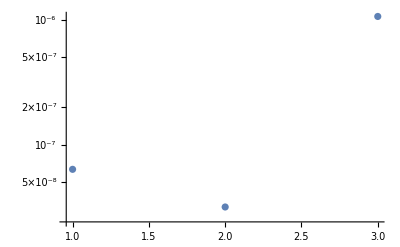

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False
]
```

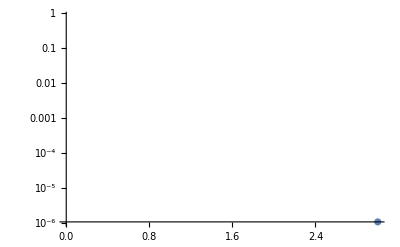

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0.8,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-20.,L2PhaseSet→-32.,S1EL_xOffset→0.,S1EL_yOffset→0.,S2EL_xOffset→0.,S2EL_yOffset→0.,S2ER_xOffset→0.,S2ER_yOffset→0.,S1ER_xOffset→0.,S1ER_yOffset→0.,Q5FFkG→-71.837,Q4FFkG→-81.251,Q3FFkG→99.225,Q2FFkG→126.35,Q1FFkG→-235.218,Q0FFkG→126.353,XC1FFkG→0.,XC3FFkG→0.,YC1FFkG→0.,YC2FFkG→0.,PDrive_mean_x→-0.0000642013,PDrive_mean_y→7.3×10^-8,PDrive_sigma_x→0.0000407835,PDrive_sigma_y→0.0000214194,PDrive_mean_xp→-0.0000856527,PDrive_mean_yp→2.516×10^-7,PDrive_median_x→-0.0000668076,PDrive_median_y→2.2×10^-9,PDrive_median_xp→-0.0000936737,PDrive_median_yp→2.181×10^-7,PDrive_sigmaSI90_x→0.0000353189,PDrive_sigmaSI90_y→0.0000218069,PDrive_sigmaSI90_z→0.000038839,PDrive_emitSI90_x→0.0000139881,PDrive_emitSI90_y→4.386×10^-6,PDrive_zCentroid→991.332,PWitness_mean_x→-0.000119949,PWitness_mean_y→-3.367×10^-7,PWitness_sigma_x→0.0000714683,PWitness_sigma_y→0.000020577,PWitness_mean_xp→-0.00011595,PWitness_mean_yp→-5.81×10^-7,PWitness_median_x→-0.000120917,PWitness_median_y→-6.317×10^-7,PWitness_median_xp→-0.000123179,PWitness_median_yp→-5.387×10^-7,PWitness_sigmaSI90_x→0.0000629028,PWitness_sigmaSI90_y→0.0000187294,PWitness_sigmaSI90_z→0.0000242938,PWitness_emitSI90_x→0.0000217368,PWitness_emitSI90_y→4.4043×10^-6,PWitness_zCentroid→991.332,bunchSpacing→-0.0000590233,transverseCentroidOffset→0.0000557495,lostChargeFraction→0.,errorTerm_lostChargeFraction→0.,errorTerm_bunchSpacing→396103.,errorTerm_transverseOffset→4.31423×10^6,errorTerm_angleOffset→0.,errorTerm_mainObjective→1.76726,maximizeMe→1.0615×10^-6|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -20.
L2PhaseSet : -32.
S1EL_xOffset : 0.
S1EL_yOffset : 0.
S2EL_xOffset : 0.
S2EL_yOffset : 0.
S2ER_xOffset : 0.
S2ER_yOffset : 0.
S1ER_xOffset : 0.
S1ER_yOffset : 0.
Q5FFkG : -71.837
Q4FFkG : -81.251
Q3FFkG : 99.225
Q2FFkG : 126.35
Q1FFkG : -235.218
Q0FFkG : 126.353
XC1FFkG : 0.
XC3FFkG : 0.
YC1FFkG : 0.
YC2FFkG : 0.
PDrive_mean_x : -0.0000642013
PDrive_mean_y : 7.3e-8
PDrive_sigma_x : 0.0000407835
PDrive_sigma_y : 0.0000214194
PDrive_mean_xp : -0.0000856527
PDrive_mean_yp : 2.516e-7
PDrive_median_x : -0.0000668076
PDrive_median_y : 2.2e-9
PDrive_median_xp : -0.0000936737
PDrive_median_yp : 2.181e-7
PDrive_sigmaSI90_x : 0.0000353189
PDrive_sigmaSI90_y : 0.0000218069
PDrive_sigmaSI90_z : 0.000038839
PDrive_emitSI90_x : 0.0000139881
PDrive_emitSI90_y : 4.386e-6
PDrive_zCentroid : 991.3318101635
PWitness_mean_x : -0.0001199492
PWitness_mean_y : -3.367e-7
PWitness_sigma_x : 0.0000714683
PWitness_sigma_y : 0.000020577
PWitness_mean_xp : -0.00011595
PWitness_mean_yp : -5.81e-7
PWitness_median_x : -0.0001209169
PWitness_median_y : -6.317e-7
PWitness_median_xp : -0.0001231786
PWitness_median_yp : -5.387e-7
PWitness_sigmaSI90_x : 0.0000629028
PWitness_sigmaSI90_y : 0.0000187294
PWitness_sigmaSI90_z : 0.0000242938
PWitness_emitSI90_x : 0.0000217368
PWitness_emitSI90_y : 4.4043e-6
PWitness_zCentroid : 991.3317511401
bunchSpacing : -0.0000590233
transverseCentroidOffset : 0.0000557495
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 396102.860580374
errorTerm_transverseOffset : 4.314227247423665e6
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 1.7672608151
maximizeMe : 1.0615e-6

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

0.0000557494

## Plot all

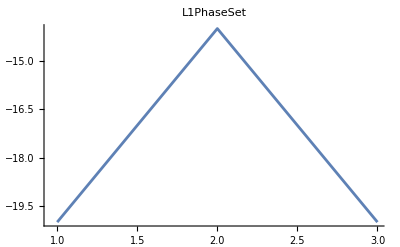
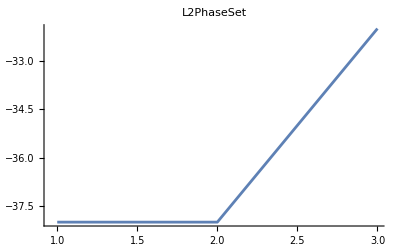
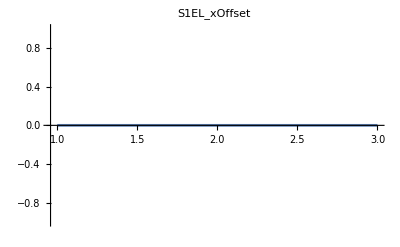
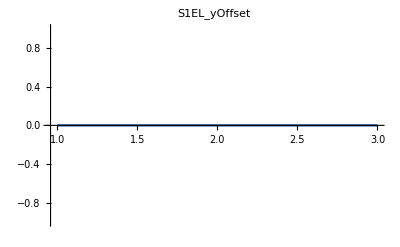
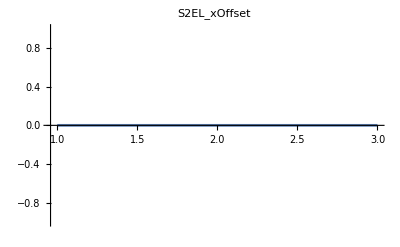
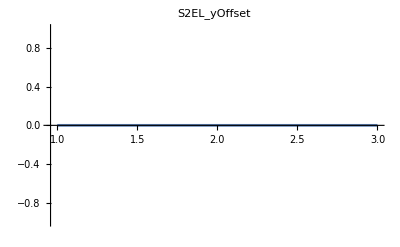
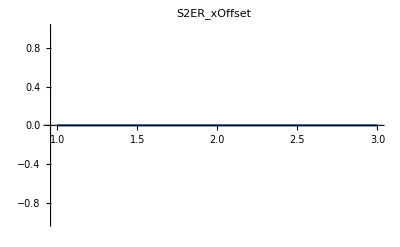
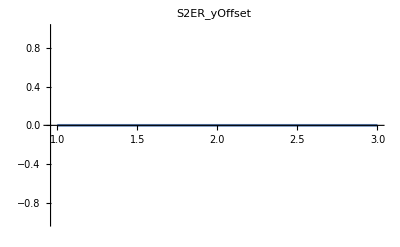
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

LinearModelFit[{{-20.,-38.,126.353,-235.218,126.35,99.225,-81.251,-71.837,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_zLen]},{-14.,-38.,126.353,-235.218,126.35,99.225,-81.251,-71.837,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_zLen]},{-20.,-32.,126.353,-235.218,126.35,99.225,-81.251,-71.837,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_zLen]}},{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG},{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}]

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVarsMathematica
]
```

{LinearModelFit[{{-20.,-38.,126.353,-235.218,126.35,99.225,-81.251,-71.837,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_zLen]},{-14.,-38.,126.353,-235.218,126.35,99.225,-81.251,-71.837,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_zLen]},{-20.,-32.,126.353,-235.218,126.35,99.225,-81.251,-71.837,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_zLen]}},{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG},{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}][BestFit],{L1PhaseSet→0.,L2PhaseSet→0.,Q0FFkG→0.,Q1FFkG→0.,Q2FFkG→0.,Q3FFkG→0.,Q4FFkG→0.,Q5FFkG→0.,S1ELxOffset→0.,S1ELyOffset→0.,S1ERxOffset→0.,S1ERyOffset→0.,S2ELxOffset→0.,S2ELyOffset→0.,S2ERxOffset→0.,S2ERyOffset→0.,XC1FFkG→0.,XC3FFkG→0.,YC1FFkG→0.,YC2FFkG→0.}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

LinearModelFit[{{-20.,-38.,126.353,-235.218,126.35,99.225,-81.251,-71.837,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_zLen]},{-14.,-38.,126.353,-235.218,126.35,99.225,-81.251,-71.837,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_zLen]},{-20.,-32.,126.353,-235.218,126.35,99.225,-81.251,-71.837,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,Missing[KeyAbsent,PDrive_zLen]}},{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG},{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}][ANOVATable]

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```